```mathematica
Quit
```

## Setup:

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dh=(1+z)h'[z]- h[z](1+q[z])==0;
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

```mathematica
(*Bella's values*)
qi = -0.647;
ji=1.035;
```

```mathematica
ϵ0=0
ϵ1=(ji-1)/(3(qi+1))
ϵ2=ji-1
ϵ3=(ji-1)/(3(qi-1/2))
```

0

0.03305

0.035

-0.0101715

#### Initial conditions for each model

```mathematica
hi = √(Ωm0(1+z0)^3+ΩL0);
Ωm0=0.3;
ΩL0=0.7;
```

```mathematica
x0=-0.001;
Ω0=0.993243;
```

```mathematica
(*q0 determined specifically for each model*)
(*z0=6;
IC0={z0,x0,Ω0,0.4859236169100545};
IC1={z0,x0,Ω0,0.5370503621671381};
IC2={z0,x0,Ω0,0.4987897437725439};
IC3={z0,x0,Ω0,0.4871436927411515};*)
```

```mathematica
(*
model 0: q(6)=0.48986486486379105 determined from z(0)=-0.55,
model 1,2,3 q(6) determiend from z(0)=-0.647
q1(6)=0.5370503621671381
q2(6) = 0.4987897437725439
q3(6)= 0.4871436927411515
*)
```

```mathematica
(*q0 determined specifically for each model*)
z0=6;
IC0={z0,x0,Ω0,0.48986486486379105};
IC1={z0,x0,Ω0,0.5370503621671381};
IC2={z0,x0,Ω0,0.4987897437725439};
IC3={z0,x0,Ω0,0.4871436927411515};
```

## Solving the system

```mathematica
z0
```

6

```mathematica
zinitial =2000;
```

### Module:

```mathematica
SolveBackground[jModel_,ICs_List, ϵVal_]:=
Module[{z0,x0,Ω0,q0,sExpr,lExpr,solFwd,solBwd, hsolFwd, hsolBwd, xFn, ΩFn, qFn, hFn},
{z0,x0,Ω0,q0}=ICs;

Block[{j,s,l, ϵ},
ϵ=ϵVal;

j[z_]=jModel;
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]/. q'[z]->Solve[dq,q'[z]][[1,1,2]]//Simplify;

(*Forward:z0->0*)
solFwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,0},PrecisionGoal->MachinePrecision][[1]];
(*Backward:z0->zinitial*)
solBwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,zinitial},PrecisionGoal->MachinePrecision][[1]];


hsolFwd=NDSolve[{dh/. solFwd,h[0]==1},{h},{z,0,z0}, PrecisionGoal->MachinePrecision][[1]];
hsolBwd=NDSolve[{dh/. solBwd,h[z0]==hsolFwd[[1,2]][z0]},{h},{z,z0,zinitial},PrecisionGoal->MachinePrecision][[1]];

xFn=With[{fwd=x/. solFwd,bwd=x/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];

ΩFn=With[{fwd=Ω/. solFwd,bwd=Ω/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];

qFn=With[{fwd=q/. solFwd,bwd=q/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];

hFn=With[{fwd=h/. hsolFwd,bwd=h/. hsolBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];
];


<|"x"->xFn,"Ω"->ΩFn,"q"->qFn,"h"->hFn,"z0"->z0, "zinitial"->zinitial|>
];
```

### Obtaining all solutions

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Model 0

```mathematica
sol0=SolveBackground[j0[z],IC0, ϵ0];
z0=sol0["z0"];
replacements0 ={x->sol0["x"], Ω->sol0["Ω"],q->sol0["q"] ,h->sol0["h"],j->j0};
SaveName=StringJoin["BackgroundSols_model0.mx"];
DumpSave[SaveName, sol0];
```

#### Model 1

```mathematica
sol1=SolveBackground[j1[z],IC1, ϵ1];
z0=sol0["z0"];
replacements1={x->sol1["x"], Ω->sol1["Ω"],q->sol1["q"] ,h->sol1["h"],j->j1};
SaveName=StringJoin["BackgroundSols_model1.mx"];
DumpSave[SaveName, sol1];
```

#### Model 2

```mathematica
sol2=SolveBackground[j2[z],IC2, ϵ2];
z0=sol0["z0"];
replacements2={x->sol2["x"], Ω->sol2["Ω"],q->sol2["q"] ,h->sol2["h"],j->j2};
SaveName=StringJoin["BackgroundSols_model2.mx"];
DumpSave[SaveName, sol2];
```

#### Model 1

```mathematica
sol3=SolveBackground[j3[z],IC3, ϵ3];
z0=sol0["z0"];
replacements3={x->sol3["x"], Ω->sol3["Ω"],q->sol3["q"] ,h->sol3["h"],j->j3};
SaveName=StringJoin["BackgroundSols_model3.mx"];
DumpSave[SaveName, sol3];
```

#### LCDM:

```mathematica
(* ΛCDM parameters *)
Ωm0=0.3;   
ΩΛ0=1-Ωm0;
hLCDM[z_]:= Sqrt[Ωm0 (1+z)^3+ΩΛ0];
HLCDM[z_]=H0 hLCDM[z];
```

```mathematica
qLCDM[z_]:=-1+(1+z)HLCDM'[z]/HLCDM[z]
```

```mathematica
(*f(R)= R:
Subscript[f, RR]=0
Subscript[f, R]=1 *)
```

```mathematica
xLCDM[z_]:=0
```

```mathematica
ΩLCDM[z_]:= (Ωm0(1+z)^3)/(Ωm0(1+z)^3+ΩΛ0)
```

```mathematica
solLCDM=<|"x"->xLCDM[z],"Ω"->ΩLCDM[z],"q"->qLCDM[z],"h"->hLCDM[z],"z0"->z0|>;
LCDMreplacements={h[z]->hLCDM[z], q[z]->qLCDM[z], j[z]->1, x[z]->xLCDM[z], Ω[z]->ΩLCDM[z]};
```

```mathematica
SaveName = StringJoin["BackgroundSols_LCDM.mx"];
DumpSave[SaveName, solLCDM];
```

## Plots:

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background solutions"];Get["BackgroundSols_model0.mx"];
Get["BackgroundSols_model1.mx"];
Get["BackgroundSols_model2.mx"];
Get["BackgroundSols_model3.mx"];
Get["BackgroundSols_LCDM.mx"];
```

```mathematica
replacements0 ={x->sol0["x"], Ω->sol0["Ω"],q->sol0["q"] ,h->sol0["h"],j->j0,ϵ->ϵ0};
replacements1 ={x->sol1["x"], Ω->sol1["Ω"],q->sol1["q"] ,h->sol1["h"],j->j1, ϵ->ϵ1};
replacements2 ={x->sol2["x"], Ω->sol2["Ω"],q->sol2["q"] ,h->sol2["h"],j->j2,ϵ->ϵ2};
replacements3 ={x->sol3["x"], Ω->sol3["Ω"],q->sol3["q"] ,h->sol3["h"],j->j3,ϵ->ϵ3};
```

### Plotting model 0

```mathematica
Get["BackgroundSols_model0.mx"];
```

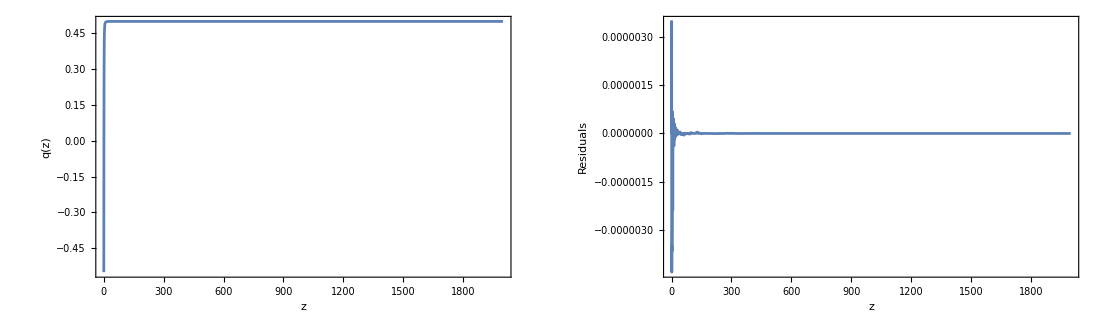

```mathematica
qplot0=Plot[Evaluate[sol0["q"][z]],{z,0,zinitial},ImageSize->400,Frame->True,FrameLabel->{"z", "q(z)"}, PlotRange->All];
qRes0=Plot[Evaluate[dq/.replacements0],{z,0,zinitial},PlotRange->All,ImageSize->400, FrameLabel->{"z", "Residuals"},  Frame->True];
qPlot0=GraphicsRow[{
qplot0, qRes0},ImageSize->1100]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/qplot.png",qPlot0];
```

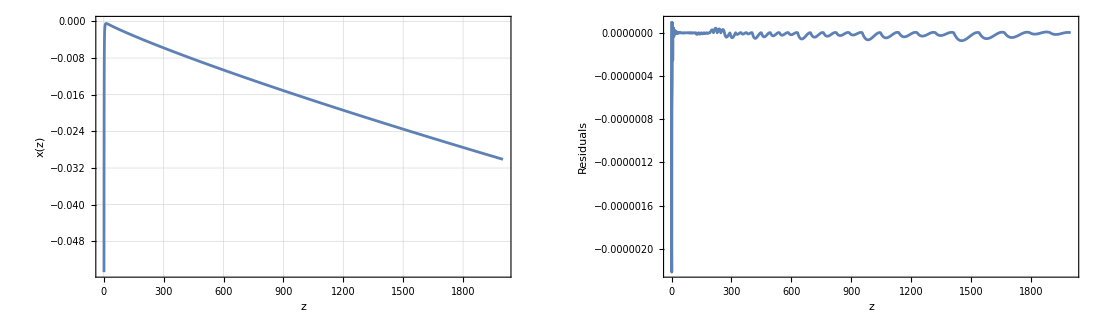

```mathematica
xplot0=Plot[Evaluate[sol0["x"][z]],{z,0,zinitial},GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"z", "x(z)"}];
xRes0=
Plot[Evaluate[dx/.replacements0],{z,0,zinitial},ImageSize->400, PlotRange->All,FrameLabel->{"z", "Residuals"}, Frame->True];
xPlot0=GraphicsRow[{
xplot0,xRes0},ImageSize->1100]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/xplot.png",xPlot0];
```

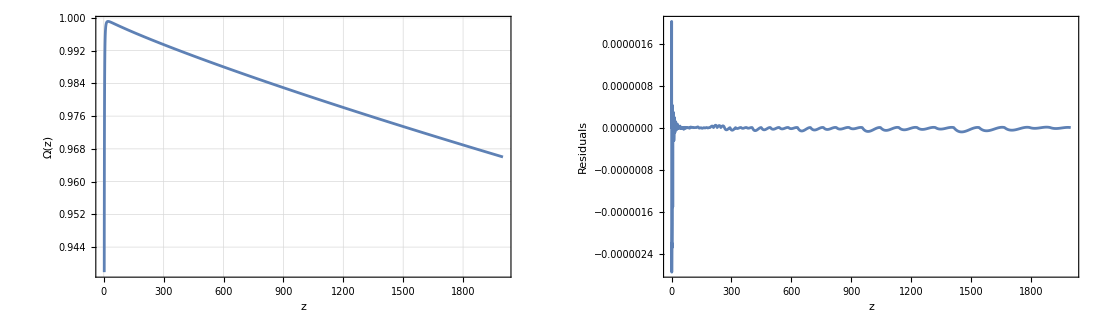

```mathematica
Oplot0=Plot[Evaluate[sol0["Ω"][z]],{z,0,zinitial},GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"z", "Ω(z)"}];
ORes0=Plot[Evaluate[dΩ/.replacements0],{z,0,zinitial},ImageSize->400, FrameLabel->{"z", "Residuals"}, Frame->True, PlotRange->All];
OPlot0=GraphicsRow[{
Oplot0, ORes0},ImageSize->1100]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/Oplot.png",OPlot0];
```

```mathematica
sol0["x"][z]
```

Piecewise[{{InterpolatingFunction[…][z], z≤6}, {InterpolatingFunction[…][z], z>6}, {0, True}}]

```mathematica
sol0["h"][z]
```

Piecewise[{{InterpolatingFunction[…][z], z≤6}, {InterpolatingFunction[…][z], z>6}, {0, True}}]

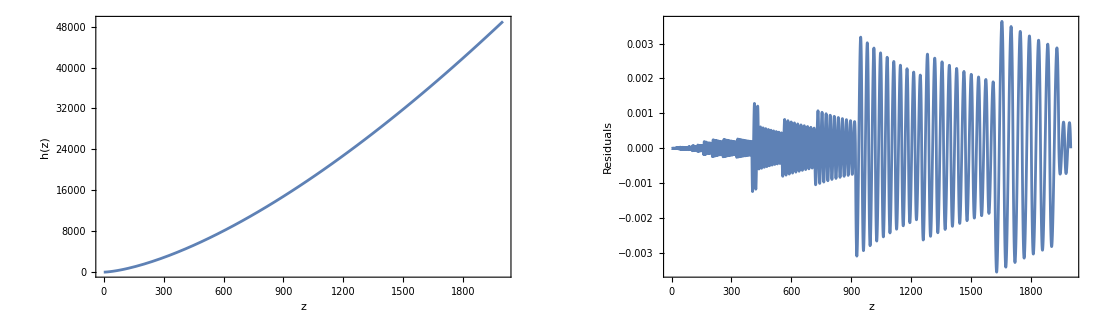

```mathematica
hplot0=Plot[Evaluate[sol0["h"][z]],{z,0,zinitial},ImageSize->400, Frame->True,FrameLabel->{"z", "h(z)"}];
hRes0=Plot[Evaluate[dh/.replacements0],{z,0,zinitial},ImageSize->400, FrameLabel->{"z", "Residuals"}, PlotRange->All, Frame->True];
hPlot0=GraphicsRow[{
hplot0, hRes0},ImageSize->1100]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/hplot.png",hPlot0];
```

#### Model 0 Errors

```mathematica
NMaximize[{Abs[dq[[1]]/.replacements0 ],0<=z<=z0},z]
Ceiling[Log10[NMaximize[{Abs[dq[[1]]/. replacements0],0<=z<=z0},z][[1]]]]
```

{0.0000149035,{z→0.291545}}

-4

```mathematica
NMaximize[{Abs[dx[[1]]/.replacements0 ],0<=z<=z0},z]
Ceiling[Log10[NMaximize[{Abs[dx[[1]]/. replacements0],0<=z<=z0},z][[1]]]]
```

{0.0000127996,{z→0.0785132}}

-4

```mathematica
NMaximize[{Abs[dΩ[[1]]/.replacements0 ],0<=z<=z0},z]
Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements0],0<=z<=z0},z][[1]]]]
```

{8.98077×10^-6,{z→0.291609}}

-5

```mathematica
NMaximize[{Abs[dh[[1]]/.replacements0 ],0<=z<=z0},z]
Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements0],0<=z<=z0},z][[1]]]]
```

{0.0000133504,{z→1.12034}}

-5

#### Model 0 Plots

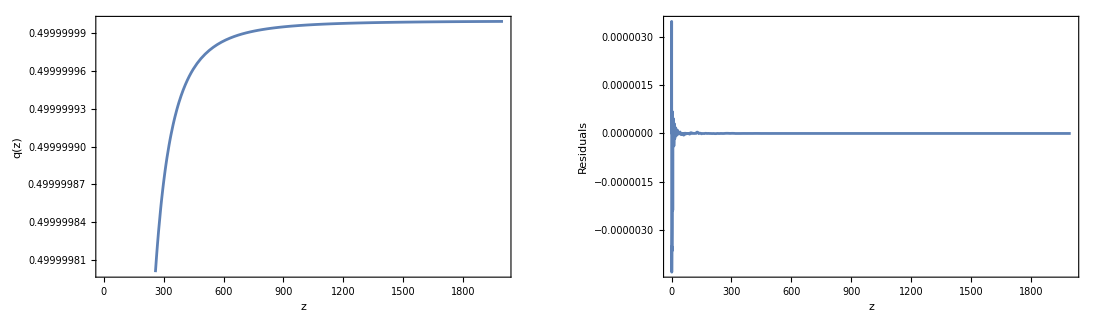

```mathematica
qPlot0
```

```mathematica
xPlot0
```

-Graphics-

```mathematica
OPlot0
```

-Graphics-

### Errors

```mathematica
errorTable=TableForm[
{{"","O(x)","O(Ω)", "O(q)"},
{"Model 0",Ceiling[Log10[NMaximize[{Abs[dx[[1]]/. replacements0],0<=z<=z0},z][[1]]]], Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements0],0<=z<=z0},z][[1]]]], 
Ceiling[Log10[NMaximize[{Abs[dq[[1]]/. replacements0],0<=z<=z0},z][[1]]]]
},
{"Model 1",Ceiling[Log10[NMaximize[{Abs[dx[[1]]/. replacements1/.replacements1/. ϵ->ϵ1],0<=z<=z0},z][[1]]]], Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements1/.replacements1/. ϵ->ϵ1],0<=z<=z0},z][[1]]]],Ceiling[Log10[NMaximize[{Abs[dq[[1]]/. replacements1/.replacements1/. ϵ->ϵ1],0<=z<=z0},z][[1]]]]
},
{"Model 2",Ceiling[Log10[NMaximize[{Abs[dx[[1]]/. replacements2/.replacements2/. ϵ->ϵ2],0<=z<=z0},z][[1]]]], Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements2/.replacements2/. ϵ->ϵ2],0<=z<=z0},z][[1]]]], Ceiling[Log10[NMaximize[{Abs[dq[[1]]/. replacements2/.replacements2/. ϵ->ϵ2],0<=z<=z0},z][[1]]]]
},
{"Model 3",Ceiling[Log10[NMaximize[{Abs[dx[[1]]/. replacements3/. replacements3/.ϵ->ϵ3],0<=z<=z0},z][[1]]]],Ceiling[Log10[NMaximize[{Abs[dΩ[[1]]/. replacements3/. replacements3/.ϵ->ϵ3],0<=z<=z0},z][[1]]]],Ceiling[Log10[NMaximize[{Abs[dq[[1]]/. replacements3/. replacements3/.ϵ->ϵ3],0<=z<=z0},z][[1]]]]
}},TableHeadings->None]
```

| O(x) | O(Ω) | O(q)
Model 0 | -4 | -5 | -4
Model 1 | -5 | -4 | -4
Model 2 | -5 | -5 | -5
Model 3 | -4 | -5 | -5

### Plotting together

```mathematica
colour=
{RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
```

#### Plotting q, x, Ω:

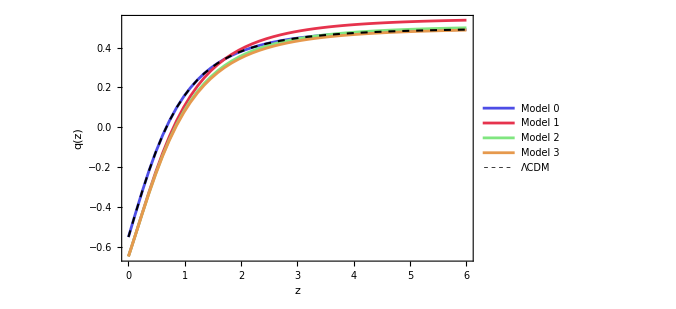

```mathematica
qplotCombined=Plot[Evaluate[{sol0["q"][z],sol1["q"][z],sol2["q"][z],sol3["q"][z], qLCDM[z]}],{z,z0,0},ImageSize->500,
Frame->True,FrameLabel->{"z","q(z)"},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}
]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/qplotCombined.png",qplotCombined];
(*"{"j = 1","j = 1 + 3ϵ(1+q)","j = 1 + ϵ","j = 1 + 3ϵ(q - 1/2)"}"*)
```

```mathematica
{sol0["q"][z],sol1["q"][z],sol2["q"][z],sol3["q"][z], qLCDM[z]}/.z->0
```

{-0.550002,-0.647001,-0.647001,-0.647001,-0.55}

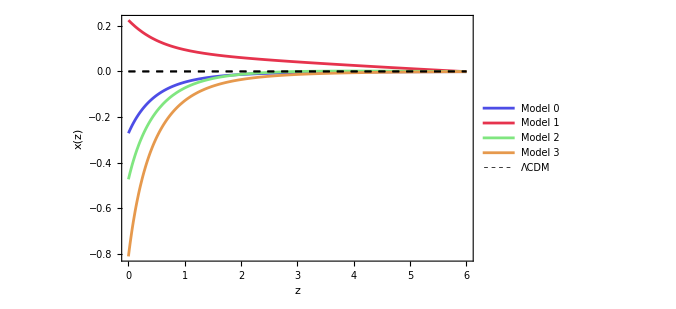

```mathematica
xplotCombined=Plot[
Evaluate[{sol0["x"][z],sol1["x"][z],sol2["x"][z],sol3["x"][z] ,xLCDM[z]}],{z,0,z0},
ImageSize->500,
Frame->True,FrameLabel->{"z","x(z)"},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
Epilog->{Dashed,Black,Line[{{0,0},{z0,0}}]},
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]

Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/xplotCombined.png",xplotCombined];
```

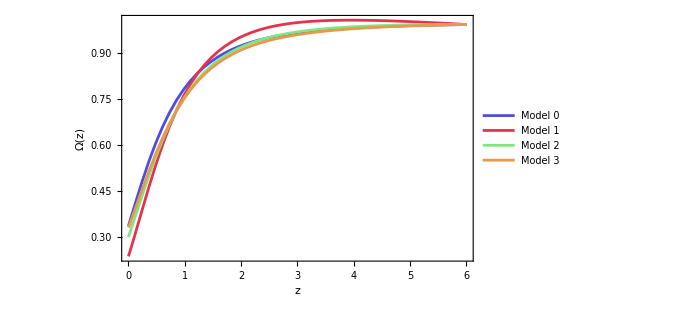

```mathematica
OplotCombined=Plot[Evaluate[{sol0["Ω"][z], sol1["Ω"][z],sol2["Ω"][z],sol3["Ω"][z]}],{z,0,z0},ImageSize->500,
Frame->True,FrameLabel->{"z","Ω(z)"},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
Epilog->{Dashed,Black,Line[{{0,0},{z0,0}}]},
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/OplotCombined.png",OplotCombined];
```

```mathematica
{sol0["Ω"][z],sol1["Ω"][z],sol2["Ω"][z],sol3["Ω"][z], ΩLCDM[z]}/.z->0
```

{0.334218,0.235093,0.298394,0.329625,0.3}

#### Plotting h, R:

```mathematica
h0[z_]=sol0["h"][z];
h1[z_]=sol1["h"][z];
h2[z_]=sol2["h"][z];
h3[z_]=sol3["h"][z];
```

```mathematica
q0[z_]=sol0["q"][z];
q1[z_]=sol1["q"][z];
q2[z_]=sol2["q"][z];
q3[z_]=sol3["q"][z];
```

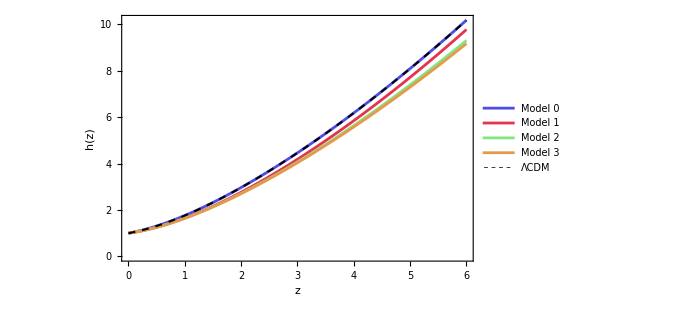

```mathematica
hplotCombined=Plot[Evaluate[{h0[z],h1[z],h2[z],h3[z], hLCDM[z]}],{z,0,z0},ImageSize->500,PlotRange->{{0,z0},{0,h0[z0]}},Frame->True,FrameLabel->{"z","h(z)"},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}
]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/hplotCombined.png",hplotCombined];
```

```mathematica
{h0[z]/hLCDM[z],h1[z]/hLCDM[z],h2[z]/hLCDM[z],h3[z]/hLCDM[z], hLCDM[z]/hLCDM[z]}/.z->1000
```

{0.999998,1.22734,0.967606,0.900059,1}

```mathematica
R[z_]= 6 h[z]^2(1-q[z]);
Rdot[z_]= 6 h[z]^3(j[z]-q[z]-2);
```

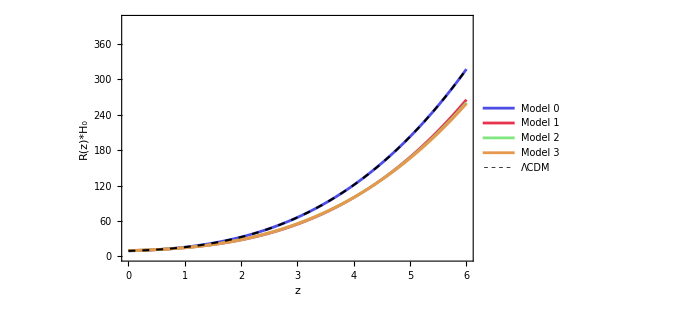

```mathematica
RplotCombined=Plot[Evaluate[{R[z]/.replacements0, R[z]/.replacements1,R[z]/.replacements2,R[z]/.replacements3,R[z]/.LCDMreplacements}],{z,0,z0},ImageSize->500,PlotRange->{{0,z0},{0,400}},Frame->True,FrameLabel->{"z","R(z)*H_0"},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.2,0.75}],PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/RplotCombined.png",RplotCombined];
```

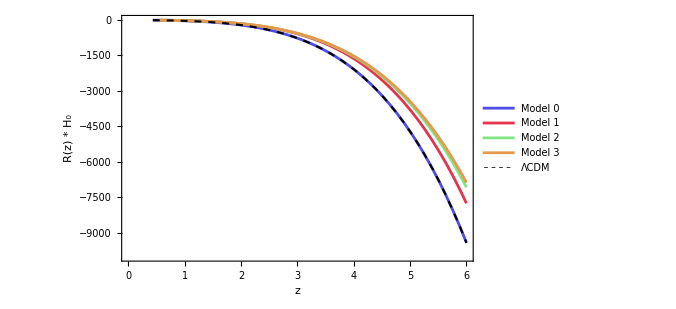

```mathematica
RDotplotCombined=Plot[Evaluate[{Rdot[z]/.replacements0,Rdot[z]/.replacements1/.replacements1,Rdot[z]/.replacements2/.replacements2,Rdot[z]/.replacements3/.replacements3,Rdot[z]/.LCDMreplacements}],{z,0,z0},
ImageSize->500,PlotRange->{{0,z0},{-10000,-10}},Frame->True,FrameLabel->{"z",Row[{OverDot["R"],"(z) * H_0"}]},
PlotLegends->Placed[
LineLegend[{"Model 0","Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.2,0.3}],PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}
]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/RdotplotCombined.png",RDotplotCombined];
```

#### Effective equation of state

```mathematica
Ωm0=0.3
```

0.3

```mathematica
Ωm[z]
```

(0.3 (1+z)^3)/h[z]^2

```mathematica
wDE[z_]:=(2q[z]-1)/(3(1-Ωm[z]));
Ωm[z_] :=Ωm0/h[z]^2(1+z)^3;
```

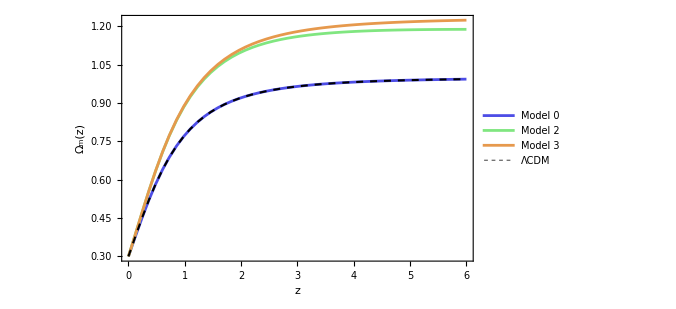

```mathematica
wDEplotCombined=Plot[Evaluate[{Ωm[z]/. replacements0,Ωm[z]/. replacements2,Ωm[z]/. replacements3,Ωm[z]/. LCDMreplacements}],{z,0,z0},ImageSize->500,
PlotRange->{{0,z0},Automatic},Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLegends->Placed[
LineLegend[{"Model 0","Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],PlotStyle->Append[colourw,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
```

```mathematica
wDE[z]
```

(-1+2 q[z])/(3 (1-(0.3 (1+z)^3)/h[z]^2))

```mathematica
colourw=
{RGBColor[0.3,0.3,0.9],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
```

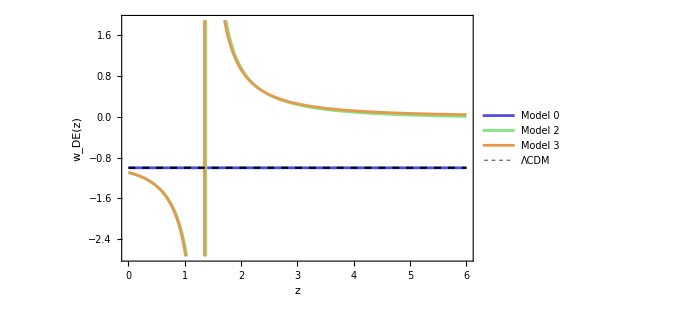

```mathematica
wDEplotCombined=Plot[Evaluate[{wDE[z]/. replacements0,wDE[z]/. replacements2,wDE[z]/. replacements3,wDE[z]/. LCDMreplacements}],{z,0,z0},ImageSize->500,
PlotRange->{{0,z0},Automatic},Frame->True,FrameLabel->{"z","w_DE(z)"},PlotLegends->Placed[
LineLegend[{"Model 0","Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],PlotStyle->Append[colourw,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/wDEplotCombined.png",wDEplotCombined];
```

```mathematica
{weff[z]/.replacements0,weff[z]/.replacements3, weff[z]/.LCDMreplacements}/.z->0
```

{weff[0],weff[0],weff[0]}

```mathematica
(*Crossing w=-1*)
Quiet@FindRoot[weff[z]+1/.replacements0, {z,5}]
Quiet@FindRoot[weff[z]+1/.replacements1, {z,5}]
Quiet@FindRoot[weff[z]+1/.replacements2, {z,5}]
Quiet@FindRoot[weff[z]+1/.replacements3, {z,5}]
```

FindRoot::nlnum: The function value {1.+weff[5.]} is not a list of numbers with dimensions {1} at {z} = {5.}.

FindRoot[weff[z]+1/.replacements0,{z,5}]

FindRoot::nlnum: The function value {1.+weff[5.]} is not a list of numbers with dimensions {1} at {z} = {5.}.

FindRoot[weff[z]+1/.replacements1,{z,5}]

FindRoot::nlnum: The function value {1.+weff[5.]} is not a list of numbers with dimensions {1} at {z} = {5.}.

FindRoot[weff[z]+1/.replacements2,{z,5}]

FindRoot::nlnum: The function value {1.+weff[5.]} is not a list of numbers with dimensions {1} at {z} = {5.}.

FindRoot[weff[z]+1/.replacements3,{z,5}]

```mathematica
wEffplotModel1=Plot[Evaluate[{weff[z]/.replacements1,weff[z]/.replacements2}],{z,0,z0},ImageSize->500,Frame->True,FrameLabel->{"z","w_eff"},PlotLegends->Placed[
LineLegend[{"Model 1", "mMdel 2"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.15}],PlotStyle->colour]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/wEffplotModel1.png",wEffplotModel1];
```

-Graphics-

```mathematica
{weff[z]/.replacements0,weff[z]/.replacements1,weff[z]/.replacements2,weff[z]/.replacements3, weff[z]/.LCDMreplacements}/.z->0
```

{weff[0],weff[0],weff[0],weff[0],weff[0]}